### Initialization of global variables and importing important structures

```mathematica
(* SET HERE THE WORKING DIRECTORY *)
SetDirectory["C:/Users/heikkie13/Work/howard_scratches/Mathematica"];
<<libs/FunctionsComplexAnalysis.m;
<<libs/FunctionsMatrixAnalysis.m;
<<libs/FunctionsFiniteGroups.m;
<<libs/FunctionsGF2.m
<<libs/FunctionsForExtraSpeciality.m;

(* This is needed for the unitary reps of symplectivc matrices: *)
(* <<"SymplecticBinary.m"; *)

(*Clear[AllBinMats];*)
dB = 10*Log[10,N[#]]&;
Clear[mm,rr];
```

These are real variables:

{a,a_n_,b,b_n_,x,x_n_,y,y_n_,x̂,(x̂)_n_,ŷ,(ŷ)_n_,r,r_n_,s,s_n_,q,q_n_,p,p_n_,ϕ,ϕ_n_,φ,φ_n_,θ,θ_n_,ϑ,ϑ_n_,χ,χ_n_,ψ,ψ_n_,ζ,ζ_n_,ρ,ρ_n_,ϱ,ϱ_n_,η,η_n_,m,n,k,l,t,f,T}

These are specifically complex variables:

{h_n,(h_n)^*,((ĥ)_n)^*,(ĥ)_n,g_n,(g_n)^*,((ĝ)_n)^*,(ĝ)_n,n_p,(n_p)^*,((n̂)_p)^*,(n̂)_p,z_n,(z_n)^*,z,z^*,w_n,(w_n)^*,w,w^*,μ_n,(μ_n)^*,ν_n,(ν_n)^*,α,α^*,β,β^*,ν,ν^*,μ,μ^*,κ,κ^*,λ,λ^*}

Note that any variable which  is not specifically real, can be expressed with *. Conjugations do not work on these, but destar does.

```mathematica
(* These are needed for functions to work properly *)
(* The dimension for the simulation must be chosen here, as multiple data structures neede by decoders etc depend on m*)
mm = 3; Nn= 2^mm; InxBin= Tuples[{0,1},{mm}]; WHn = WHmatrix[Nn]/Sqrt[Nn];  InitializeVeryBare[mm];
ZeroVecm = Table[0,{mm}];
PermMatEShifts = TensorMany[Join[Table[unit2,{#}],{sigx},Table[unit2,{mm-1-#}]]] &/@ (Range[mm]-1); PermMatEShifts //mfl;
```

### Codebook

```mathematica
GenerateChirp = Module[{Sint, bvec,xvec},Sint = #1; bvec = #2;
(xvec  = IntegerDigits[#-1,2,mm];
I^(xvec.Sint.xvec + 2 bvec.xvec)/Sqrt[2^mm]) &/@ Range[2^mm]
]&;

MakeUnitaryFromSymmetric = Module[{Sint,cvec,dvec,Ord2},Sint = #;
 (cvec = IntegerDigits[#-1,2,mm];
Ord2 = cvec.Sint.cvec;
(dvec  = IntegerDigits[#-1,2,mm];
I^(Ord2 + 2 dvec.cvec)/Sqrt[2^mm]
) &/@ Range[2^mm]
) &/@ Range[2^mm] ]&; 

(* UNCOMMENT below if you need to run quantization simulation *)


AllBinSymm = GenerateSn2[mm];
AllUmats = MakeUnitaryFromSymmetric[#] &/@ AllBinSymm;
AllUmats // mfl;

CB  = Transpose[Sequence@@(Transpose[#]) &/@ AllUmats]; card = Length[CB[[1]]]; {Length[AllUmats],card}
```

{64,512}

#### Extended codebook

```mathematica
(* Creates upper triangular matrix from vector *)
upperTriangular[v_]:=upperTriangular[v,(1+Sqrt[1+8*Length@v])/2]
upperTriangular[v_,n_]:=Module[{i=0},Array[If[#>=#2,0,v[[++i]]]&,{n,n}]]
upperTriangulizer[n_Integer,type_:_Integer]:=Module[{v,r},Quiet[With[{r=upperTriangular[v,n]},Compile[{{v,type,1}},r]],Part::partd]]
(* Example printed below *)
upperTriangulizer[3] @ Range[3] // MatrixForm

(* Generates the set of (size X size) symmetric matrices with binary diagonal and off-diagonal elements belong to {0, 1/2, 1, 3/2} *)
ExtendedSymmetricMats=Module[{size, diag, diagmat, triuvec, triumat, result, results, inx},size=#;
results={};
(inx=#;
diag=IntegerDigits[Mod[inx,2^size],2,size];
diagmat=DiagonalMatrix[diag];
triuvec=IntegerDigits[Floor[inx/(2^size)],4, (size - 1)*size / 2];
triumat=(upperTriangulizer[size]@triuvec)/2;
result=triumat+Transpose[triumat]+diagmat;
AppendTo[results,result];)&/@Range[0,2^(size^2)-1];
results
]&;

RandomExtendedSymmetricMat = Module[{size, diag, diagmat, triuvec, triumat, result, inx},size=#;
inx = RandomInteger[{0, 2^(size^2)-1}];
diag=IntegerDigits[Mod[inx,2^size],2,size];
diagmat=DiagonalMatrix[diag];
triuvec=IntegerDigits[Floor[inx/(2^size)],4, (size - 1)*size / 2];
triumat=(upperTriangulizer[size]@triuvec)/2;
result=triumat+Transpose[triumat]+diagmat;
result
]&;

CreateCoverMats = Module[{results, inx, triuvec, size, triumat, result}, size = #;
results={};
(inx=#;
triuvec=IntegerDigits[Floor[inx],2, (size - 1)*size / 2];
triumat=(upperTriangulizer[size]@triuvec)/2;
result=triumat+Transpose[triumat];
AppendTo[results,result];
)&/@Range[0,2^((size-1)*size/2)-1];
results
]&;
```

(0 | 1 | 2
0 | 0 | 3
0 | 0 | 0)

```mathematica
CoverSmats = CreateCoverMats[mm];
```

```mathematica
(* UNCOMMENT below if you need to run quantization simulation *)



ExtendedSmats = ExtendedSymmetricMats[mm]; ExtendedSmats // mfl;
ExtendedUmats = MakeUnitaryFromSymmetric[#] &/@ ExtendedSmats; ExtendedUmats //mfl;
(* The matrices are unitary in the extended set *)
Union[MapThread[Dot, {ExtendedUmats,(ConjugateTranspose[#] &/@ ExtendedUmats)}]] // mfl
ExtendedCB  = Transpose[Sequence@@(Transpose[#]) &/@ ExtendedUmats];card = Length[ExtendedCB[[1]]]; {Length[ExtendedUmats],card}
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

{512,4096}

#### Minimal distances

```mathematica
(* WARNING, THIS IS INTENSIVE TO CALCULATE FOR mm > 2 *)

(* UNCOMMENT TO RUN *)

(*
innerprods = ConjugateTranspose[ExtendedCB].ExtendedCB; 
chorddists = Sqrt[1 - Abs[innerprods]^2];
chorddistflatten = chorddists // Flatten // Union;
(* Minimal distance of the extended codebook in terms of chordal distance *)
Print["Extended codebook has minimal chordal distance: ",FullSimplify[Min[Complement[chorddistflatten, {0}]]], " ≈ " , Min[Complement[chorddistflatten, {0}]] // N ]

innerprodsOrig = ConjugateTranspose[CB].CB; 
chorddistsOrig = Sqrt[1 - Abs[innerprodsOrig]^2];
chorddistflattenOrig = chorddistsOrig // Flatten // Union;
(* Minimal distance of the extended codebook in terms of chordal distance *)
Print["Vanilla BC codebook has minimal chordal distance: ", Min[Complement[chorddistflattenOrig, {0}]], " ≈ ", Min[Complement[chorddistflattenOrig, {0}]]// N ]
*)
```

## Decoders

### Extended decoders

```mathematica
ExtendedDecoderBf=Module[{vecin,squared,Sest,best,MaskS,MaskChirp,UnmaskedChirp,zleft,metric,vecest, SquaredCandidates, BaseChirp, Candidates, Shat, bhat, zhat, metrichat, Peakinxs},vecin=#1; K = #2;
squared=vecin*vecin;
squared=squared/Norm[squared];
{Shat, bhat, zleft, metric}=BreadthFirstDecoding[squared,K, True, Range[mm]];
Candidates = {};
MaskS=Shat/2 + DiagonalMatrix[bhat];
MaskChirp= GenerateChirp[MaskS ,ZeroVecm];
UnmaskedChirp=vecin*Conjugate[MaskChirp];
UnmaskedChirp=UnmaskedChirp/Norm[UnmaskedChirp];
{Sest, best, zleft, metric} = BreadthFirstDecoding[UnmaskedChirp, K, True, Range[mm]];
{Sest +MaskS, best, zleft, metric}
]&;

ExtendedDecoderBfEnforceZeroDiagonal=Module[{vecin,squared,Sest,best,MaskS,MaskChirp,UnmaskedChirp,zleft,metric,vecest, SquaredCandidates, BaseChirp, Candidates, Shat, bhat, zhat, metrichat, Peakinxs},vecin=#1; K = #2;
squared=vecin*vecin;
squared=squared/Norm[squared];
{Shat, bhat, zleft, metric}=BreadthFirstDecodingZeroDiagonal[squared,K, True, Range[mm]];
Candidates = {};
MaskS=Shat/2 + DiagonalMatrix[bhat];
MaskChirp= GenerateChirp[MaskS ,ZeroVecm];
UnmaskedChirp=vecin*Conjugate[MaskChirp];
UnmaskedChirp=UnmaskedChirp/Norm[UnmaskedChirp];
{Sest, best, zleft, metric} = BreadthFirstDecoding[UnmaskedChirp, K, True, Range[mm]];
{Sest +MaskS, best, zleft, metric}
]&;
```

### Pitaval & Qin ChirpRA

```mathematica
ExtendedChirpRA = Module[{vecin, Sbar, CoverSequence, ybar, Sest, R, PermMatEsh, avec, bvec, zvec, Abses, mu, largestmu, Peaki, best, Svec, Scandidate, cvec, xvec, Wht,PhaseVec}, vecin = #;
largestmu = 0;
Scandidate = {};
(Sbar = #;
CoverSequence = GenerateChirp[-1*Sbar, ZeroVecm];
ybar = vecin * CoverSequence;
Sest = Table[0,mm,mm];
mu = 0;
(R = #;
PermMatEsh =  PermMatEShifts[[R]];
avec = ZeroVecm; avec[[R]]=1;
PhaseVec = (bvec = IntegerDigits[#-1,2,mm]; I^(-avec.bvec)) &/@ Range[Nn];
zvec =Sqrt[Nn]* PhaseVec*DiscreteHadamardTransform[Conjugate[ybar] * (PermMatEsh.ybar), Method -> "BitComplement"];
Abses = Abs[zvec];
Peaki = Ordering[Abses,-1][[1]];
Svec  = IntegerDigits[Peaki-1,2,mm];
Sest[[R]] = Svec;
mu = mu + Abses[[Peaki]];
)&/@ Range[mm];
If[mu > largestmu,
Scandidate = Sest + Sbar;
largestmu = mu;
];
)&/@ CoverSmats;
cvec = GenerateChirp[-1*Scandidate, ZeroVecm];
xvec = cvec * vecin;
Abses = Abs[DiscreteHadamardTransform[xvec, Method -> "BitComplement"]];
Peaki = Ordering[Abses, -1][[1]];
best = IntegerDigits[Peaki - 1, 2, mm];
{Scandidate, best, largestmu}
]&;
```

### Truth table calculators and decoding order

```mathematica
DecodingOrder = Module[{vecin, maxis, PermMatEsh, abses, permutetable, inx}, vecin = #;
maxis = {};
(inx = #;
	PermMatEsh =  PermMatEShifts[[inx]];
	abses = Abs[ Nn*(Conjugate[vecin]*(PermMatEsh.vecin)).WHn];
	maxis  = Append[maxis, Max[abses]];
) &/@ Range[mm];
Reverse[Ordering[maxis]]
]&;

GiveTruthTable = Module[{index, size, basetable, binary}, input=#;
index = #1;
size = #2;
binary = Mod[Floor[(Range[2^size] - 1) / 2^(size -index)], 2];
Table[binary[[i]] == 0, {i, 1, 2^size}]
]&;

UpdateTruthTable = Module[{Tt,Tt2, R},
Tt = #1;
R = #2;
Tt2 = GiveTruthTable[R, mm];
Table[Tt[[i]] && Tt2[[i]], {i, 1, Length[Tt]}]
]&;
```

### Row decoders

```mathematica
DecodeRowList = Module[{start, PauliMat, Metrics, Results, Projectedvectors, Peaks, Peaki, Peakinxs, Sestk, Metrick, Signbitsall, projectedvectors, Sests, Sest, R, K, RangeNow, Tt, vecrot, NewK,  Signbits, Svec, Signbitsk, Sigmak, veck, Mu, WithProjections, avec, bvec, PhaseVec, PermMatEsh, Wht, vecin, Abses, Signs},
Sest = #1;
Signbits = #2;
vecin = #3;
Mu = #4;
Tt = #5;
WithProjections = #6;
K = #7;
R = #8;
start = Transpose[Sest][[R]];
RangeNow=Pick[Range[2^mm],Tt] + FromDigits[start,2];
(* In the end K might be greater than the number of possible different rows *)
NewK = Min[K, Length[RangeNow]];
(* This normalizes out the phase i^{e_i.S.e_i^T} *)
avec = ZeroVecm; avec[[R]]=1;
PhaseVec = (bvec = IntegerDigits[#-1,2,mm]; I^(-avec.bvec)) &/@ Range[Nn];
PermMatEsh =  PermMatEShifts[[R]];
Wht =  Sqrt[Nn]PhaseVec*DiscreteHadamardTransform[Conjugate[vecin]*(PermMatEsh.vecin), Method->"BitComplement"] // Chop;
Abses = Abs[Wht];
Signs = Sign[Wht];
Metrics = {};
Signbitsall = {};
Projectedvectors = {};
Sests = {};

Peakinxs = Take[Select[Reverse[Ordering[Abses]], MemberQ[RangeNow, #]&], NewK];
Results = (
Peaki = #;
(* Mathematica copies arrays by default so no worries of reference problems *)
Sestk = Sest;
If[WithProjections, Metrick = (Mu + Abses[[Peaki]]) / 2;, Metrick = (Mu + Abses[[Peaki]]);];
Sigmak = Signs[[Peaki]];
Signbitsk = Signbits; 
Signbitsk[[R]] =(1 - Sigmak) / 2;
Svec  = IntegerDigits[Peaki-1,2,mm];
Sestk[[R]]=Svec;
If[WithProjections, avec = ZeroVecm; avec[[R]]=1;
PauliMat = MakePauli[avec,Svec];
vecrot = vecin.PauliMat;
veck = (vecin + Sigmak * vecrot) / 2;
, 
(* This runs if withProjections = False *)
veck = vecin;
];
{Sestk, Signbitsk,veck, Metrick}
)&/@ Peakinxs;
Results
]&;

DecodeRowListZeroDiagonal = Module[{start, PauliMat, Metrics, Results, Projectedvectors, Peaks, Peaki, Peakinxs, Sestk, Metrick, Signbitsall, projectedvectors, Sests, Sest, R, K, RangeNow, Tt, vecrot, NewK,  Signbits, Svec, Signbitsk, Sigmak, veck, Mu, WithProjections, avec, bvec, PhaseVec, PermMatEsh, Wht, vecin, Abses, Signs},
Sest = #1;
Signbits = #2;
vecin = #3;
Mu = #4;
Tt = #5;
WithProjections = #6;
K = #7;
R = #8;
start = Transpose[Sest][[R]];
Tt = UpdateTruthTable[Tt, R];
RangeNow=Pick[Range[2^mm],Tt] + FromDigits[start,2];
(* In the end K might be greater than the number of possible different rows *)
NewK = Min[K, Length[RangeNow]];
(* This normalizes out the phase i^{e_i.S.e_i^T} *)
avec = ZeroVecm; avec[[R]]=1;
PhaseVec = (bvec = IntegerDigits[#-1,2,mm]; I^(-avec.bvec)) &/@ Range[Nn];
PermMatEsh =  PermMatEShifts[[R]];
Wht =  Sqrt[Nn]PhaseVec*DiscreteHadamardTransform[Conjugate[vecin]*(PermMatEsh.vecin), Method->"BitComplement"] // Chop;
Abses = Abs[Wht];
Signs = Sign[Wht];
Metrics = {};
Signbitsall = {};
Projectedvectors = {};
Sests = {};

Peakinxs = Take[Select[Reverse[Ordering[Abses]], MemberQ[RangeNow, #]&], NewK];
Results = (
Peaki = #;
(* Mathematica copies arrays by default so no worries of reference problems *)
Sestk = Sest;
If[WithProjections, Metrick = (Mu + Abses[[Peaki]]) / 2;, Metrick = (Mu + Abses[[Peaki]]);];
Sigmak = Signs[[Peaki]];
Signbitsk = Signbits; 
Signbitsk[[R]] =(1 - Sigmak) / 2;
Svec  = IntegerDigits[Peaki-1,2,mm];
Sestk[[R]]=Svec;
If[WithProjections, avec = ZeroVecm; avec[[R]]=1;
PauliMat = MakePauli[avec,Svec];
vecrot = vecin.PauliMat;
veck = (vecin + Sigmak * vecrot) / 2;
, 
(* This runs if withProjections = False *)
veck = vecin;
];
{Sestk, Signbitsk,veck, Metrick}
)&/@ Peakinxs;
Results
]&;
```

### List decoder

```mathematica
BreadthFirstDecoding = Module[{vecin, K, R, Peakinxs,  WithProjections, Orderation, Tt, Sest, Candidatelist, Newcandidates, vecest, inners, cvec, best},
vecin = #1;
K = #2;
WithProjections = #3;
Orderation = #4;
Tt = Table[True, 2^mm];
Sest = Table[0,{mm},{mm}];
Candidatelist = {{Table[0,{mm},{mm}], Table[0, mm], vecin, Norm[vecin]^2}};
(
R = Orderation[[#]];
Newcandidates = {};
(Newcandidates = Join[Newcandidates,DecodeRowList @@ Join[#, {Tt, WithProjections, K, R}]]; )&/@Candidatelist;
Peakinxs = Take[Reverse[Ordering[Newcandidates[[All, 4]]]], Min[K, Length[Newcandidates]]];
Candidatelist = Newcandidates[[Peakinxs]];
Tt = UpdateTruthTable[Tt, R];
)&/@Range[mm];

If[WithProjections, posi = 1, inners = (best = #[[2]]; Sest = #[[1]];
vecest = (cvec = IntegerDigits[#-1,2,mm];I^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];
Abs[Conjugate[vecin].vecest]
) &/@ Candidatelist;
posi = Position[inners,Max[inners]][[1,1]]; ];
Candidatelist[[posi]]
]&;

BreadthFirstDecodingZeroDiagonal = Module[{vecin, K, R, Peakinxs,  WithProjections, Orderation, Tt, Sest, Candidatelist, Newcandidates, vecest, inners, cvec, best},
vecin = #1;
K = #2;
WithProjections = #3;
Orderation = #4;
Tt = Table[True, 2^mm];
Sest = Table[0,{mm},{mm}];
Candidatelist = {{Table[0,{mm},{mm}], Table[0, mm], vecin, Norm[vecin]^2}};
(
R = Orderation[[#]];
Newcandidates = {};
(Newcandidates = Join[Newcandidates,DecodeRowListZeroDiagonal @@ Join[#, {Tt, WithProjections, K, R}]]; )&/@Candidatelist;
Peakinxs = Take[Reverse[Ordering[Newcandidates[[All, 4]]]], Min[K, Length[Newcandidates]]];
Candidatelist = Newcandidates[[Peakinxs]];
Tt = UpdateTruthTable[Tt, R];
)&/@Range[mm];

If[WithProjections, posi = 1, inners = (best = #[[2]]; Sest = #[[1]];
vecest = (cvec = IntegerDigits[#-1,2,mm];I^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];
Abs[Conjugate[vecin].vecest]
) &/@ Candidatelist;
posi = Position[inners,Max[inners]][[1,1]]; ];
Candidatelist[[posi]]
]&;

BreadthFirstDecodingGiveList = Module[{vecin, K, R, Peakinxs,  WithProjections, Orderation, Tt, Sest, Candidatelist, Newcandidates, vecest, inners, cvec, best},
vecin = #1;
K = #2;
WithProjections = #3;
Orderation = #4;
Tt = Table[True, 2^mm];
Sest = Table[0,{mm},{mm}];
Candidatelist = {{Table[0,{mm},{mm}], Table[0, mm], vecin, Norm[vecin]^2}};
(
R = Orderation[[#]];
Newcandidates = {};
(Newcandidates = Join[Newcandidates,DecodeRowList @@ Join[#, {Tt, WithProjections, K, R}]]; )&/@Candidatelist;
Peakinxs = Take[Reverse[Ordering[Newcandidates[[All, 4]]]], Min[K, Length[Newcandidates]]];
Candidatelist = Newcandidates[[Peakinxs]];
Tt = UpdateTruthTable[Tt, R];
)&/@Range[mm];
Candidatelist
]&;
```

## Simulation

### Quantization simulation

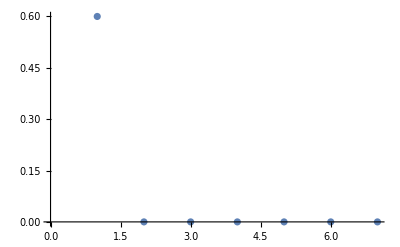

```mathematica
(* Quantization simulation is commented by default *)

drops = 5;
Ktable = {1,2,3,4,5,20,512};
Errortable ={};
(K = #;
errors = 0;
(
(*tstvec = {1,I}.RandomVariate[NormalDistribution[0,1],{2,Nn}]; tstvec = tstvec/Norm[tstvec];*)
tstvec = E^(I*2Pi*RandomReal[10, Nn]); tstvec = tstvec/Norm[tstvec];
inners = Abs[Conjugate[tstvec].CB];
posi = Position[inners,Max[inners]][[1,1]];
ClosestVec = Transpose[CB][[posi]];

{Sest, best, zleft, metric} = BreadthFirstDecoding[tstvec, K,True, Range[mm]];Sest //mf;
vecest = (cvec = IntegerDigits[#-1,2,mm];I^(cvec.Sest.cvec + 2*best.cvec)) &/@ Range[Nn]; vecest  = vecest/Norm[vecest];
Dist2 = 1-Abs[ClosestVec.Conjugate[vecest]]^2 ;
If[Abs[ClosestVec.Conj[vecest]]<= 0.99,errors = errors+1];
)&/@ Range[drops];
AppendTo[Errortable, errors];
)&/@Ktable;
ListPlot[Errortable/drops]
```

### Communication simulation

{2.28125,Null}

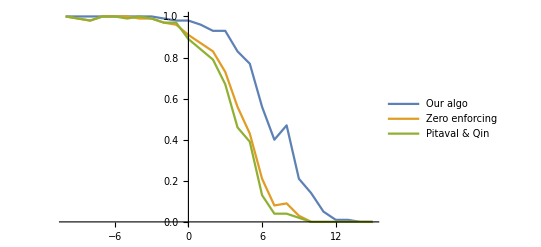

```mathematica
(* DIFFERENT BF ALGOS FOR EXTENDED BCS *)

(* TODO: 
1) Compare when to decode the diagonal, before or after.
 2) Force diagonal to be 0?
   3) Run performance tests: which values for mm are feasible.
*)
drops = 100;
SNRValues =  Range[-10,15,1];
BfResults =Table[0, Length[SNRValues]];
BfZeroDiagResults =Table[0, Length[SNRValues]];
ResultsExtendedRA = Table[0, Length[SNRValues]];
SetSharedVariable[BfResults];
SetSharedVariable[BfZeroDiagResults];
SetSharedVariable[ResultsExtendedRA];
Timing[
ParallelDo[
SNR = SNRValues[[loopind]];
gamma = 10^(SNR/10);
errors = {0,0,0};
(
Smatrix = RandomExtendedSymmetricMat[mm];
bvector = RandomChoice[{0,1}, mm];
chirp = GenerateChirp[Smatrix, bvector];
tstvec = Sqrt[Nn*gamma]*chirp + {1,I}.RandomVariate[NormalDistribution[0,1],{2,Nn}]/Sqrt[2];
tstvec = tstvec/Norm[tstvec];
{Sestimate,bestimate,zleft, metric}=ExtendedDecoderBf[tstvec,2];
If[Union[Flatten[Sestimate-Smatrix]]!={0} || Union[bestimate-bvector]!={0},errors[[1]] = errors[[1]]+1];

{Sestimate,bestimate,zleft, metric}=ExtendedDecoderBfEnforceZeroDiagonal[tstvec,2];
If[Union[Flatten[Sestimate-Smatrix]]!={0} || Union[bestimate-bvector]!={0},errors[[2]] = errors[[2]]+1];

{Sestimate, bestimate, metric} = ExtendedChirpRA[tstvec];
If[Union[Flatten[Sestimate-Smatrix]]!={0} || Union[bestimate-bvector]!={0},errors[[3]] = errors[[3]]+1];
)&/@ Range[drops];
errorprobs = errors/drops//N;
BfResults[[loopind]] = {SNR, errorprobs[[1]]};
BfZeroDiagResults[[loopind]] = {SNR, errorprobs[[2]]};
ResultsExtendedRA[[loopind]] ={SNR, errorprobs[[3]]};,
{loopind, Length[SNRValues]}
]]
ListLinePlot[{BfResults, BfZeroDiagResults, ResultsExtendedRA},PlotLegends->{"Our algo","Zero enforcing", "Pitaval & Qin"}]
```

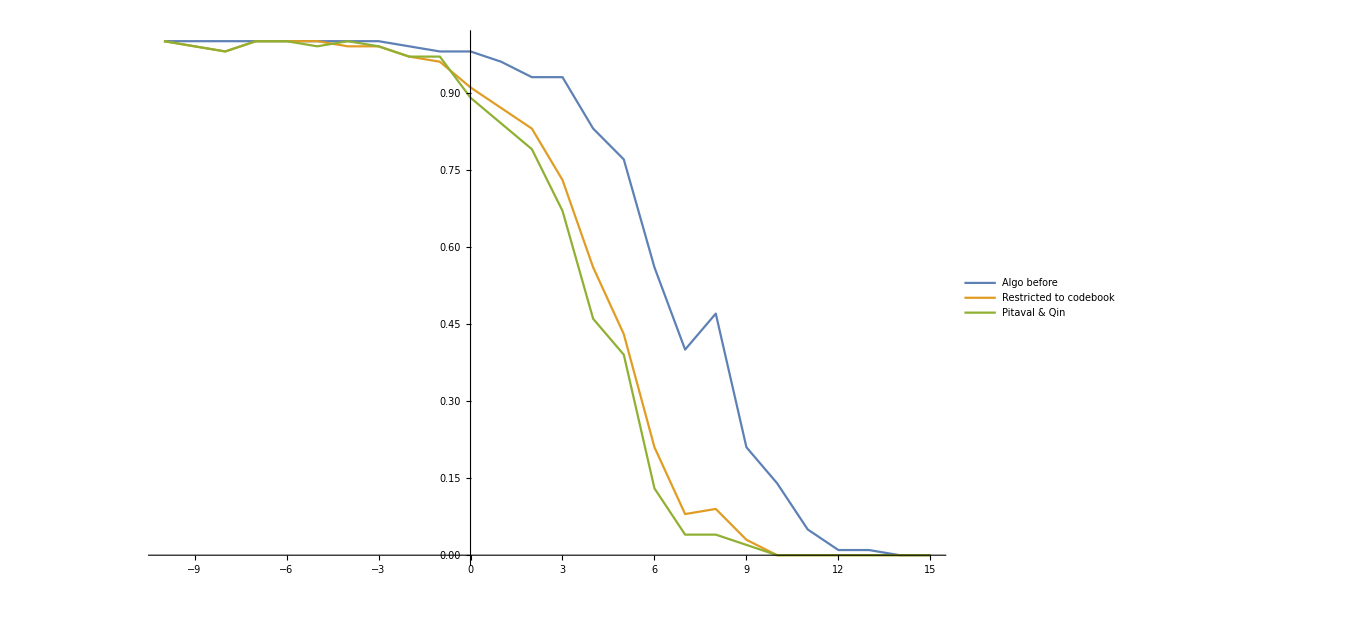

```mathematica
p1 = ListLinePlot[{BfResults,BfZeroDiagResults, ResultsExtendedRA},PlotLegends->{"Algo before", "Restricted to codebook", "Pitaval & Qin"}, ImageSize->{1000,1000}]
```

```mathematica
Export[StringJoin["figs/howard_",StringReplace[DateString[{"Year","-","Month","-","Day", "-", "Time"}], ":"->"_"],".png"], p1];
```